# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: All packages

```mathematica
(* We move the image so intermediate cyclopean image haves bigger reach *)
dis=0;
ic=move[ib,dis]
steps=0.5;
```

-Graphics-

```mathematica
row=10;
lvlmin=1;
lvlmax=3;

pyrfiac=pyrfi[ia,ic,row,lvlmax];


e=0.05;
```

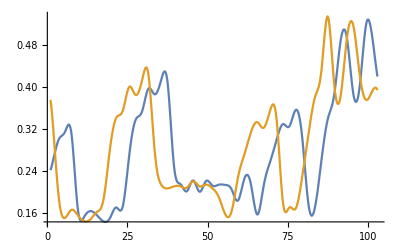

```mathematica
p0=46;
Plot[{pyrfiac[[2,1,1]][x],pyrfiac[[2,2,1]][x]},{x,1,103}]
```

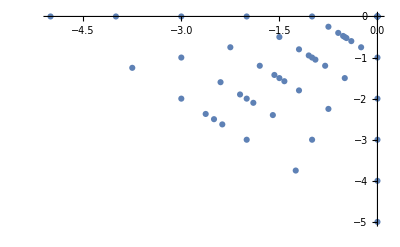

```mathematica
(* Creating list of values for v0 *)
rangev0=Range[-5,0];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
(* See list of values for v0 *)
ListPlot[listv0]
```

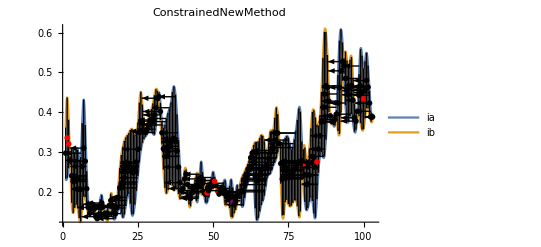

```mathematica
seeAllLine[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],0.001,"ConstrainedNewMethod"]
```

```mathematica
ress=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],0.001,"ConstrainedNewMethod"];
```

```mathematica
res=Select[ress,#[[3]]=="converged"&];
```

```mathematica
Dimensions[res];
```

```mathematica
realp=res[[All,4]]-res[[All,1]];
```

```mathematica
index=DeleteDuplicates[Round[realp]];
(* Amount of cyclopean index capacity *)
Dimensions[index]
```

{61}

```mathematica
realPV=Flatten[{realp,-(Total[#]&/@res[[All,1;;2]])+dis},{{2},{1}}];
```

```mathematica
combinePV[realPV_]:=Block[{srtDistinctPV,newPV,i,c,sum,solution},(

srtDistinctPV=Sort[DeleteDuplicates[Round[realPV[[All,1]]]]];

newPV=SortBy[Flatten[{Round[realPV[[All,1]]],realPV[[All,2]]},{{2},{1}}],First];

i=1;

Table[
c=0;
sum=0;

While[newPV[[i,1]]==p, 
sum=newPV[[i,2]]+sum;
c=c+1;
i=i+1;
solution={p,sum/c}
];
solution

,{p,srtDistinctPV}]

)]
```

```mathematica
resPV=combinePV[realPV]
```

Part::partw: Part 195 of {{5,3.04008},{6,5.24826},{8,5.42231},{8,5.42276},{8,5.42535},{8,5.43529},{8,5.43723},{8,5.44249},{8,5.4435},{8,5.44948},«184»} does not exist.

{{5,3.04008},{6,5.24826},{8,5.44549},{9,5.6259},{12,5.46188},{13,5.56482},{14,5.46763},{16,5.45839},{17,5.54146},{18,5.36918},{20,5.33542},{21,5.45439},{22,5.70696},{25,6.25592},{26,6.24208},{28,6.24139},{29,6.25764},{30,6.17022},{31,6.12197},{32,6.02335},{33,6.06933},{35,5.99563},{36,5.92992},{38,5.5901},{39,5.57959},{40,5.37727},{41,5.11073},{44,5.47671},{45,4.6121},{46,5.25239},{47,5.3405},{49,5.59432},{50,5.36018},{51,5.44157},{53,5.7212},{57,5.13455},{58,5.18028},{59,5.32621},{61,2.2071},{67,8.63482},{68,8.56355},{69,8.7087},{70,8.76278},{71,8.8074},{72,8.69156},{74,8.3654},{75,8.31997},{77,8.4808},{80,7.52948},{85,5.46228},{87,5.27456},{88,5.26825},{90,5.40562},{91,5.33005},{93,5.22557},{94,1.13505},{95,5.42399},{96,5.43468},{98,5.43477},{99,5.32993},{102,5.2626}}

```mathematica
ListPlot[{ImageData[id][[row]],resPV},PlotLabels->{"Real","Rounded"},Joined->True,Mesh->All,PlotRange->{{1,103},{0,10}}]
```

-Graphics-